Calculate semiconductor optical channel waveguide modes via the effective index method 
Prof. Charlie Ironside
Department of Physics and Astronomy
Curtin University 
Bentley Campus,
Western Australia 6102
email: Charlie.Ironside@curtin.edu.au
web page address:http://oasisapps.curtin.edu.au/staff/profile/view/Charlie.Ironside
Included in the book : “Semiconductor Integrated Optics for Switching Light” by Charlie Ironside 
References
 "An Introduction to Optical Waveguides" M. J. Adams
 "Electromagnetic Principles of Integrated Optics" D. L. Lee
 
 The program use the effective index method to calculate the type of electro-magnetic wave propagation that an optical waveguide can support  -it calculates the propagation constants in the x, y and z directions for a 3 layered waveguide  
 
 Figure of waveguide geometry showing layers and co-ordinates for xz plane
 
 
Figure of waveguide geometry showing layers and co-ordinates for yz plane 

 -Graphics-
Figure (4.11) from “Electromagnetic Principles of Integrated Optics” D. L. Lee
Warning: Before using this notebook it’s important to have a good understanding of the effective index method (see the references particularly “Electromagnetic Principles of Integrated Optics” D. L. Lee -it’s particularly important to understand the B versus v figure (figure 4.11 of LEE’s book). Be aware that if v>3 then there is more than one mode that can be supported by the waveguide.

```mathematica
(*The effective index method for a Channel Dielectric waveguide*)
(*-see Lee's book Chapter 4 & 5 *)

μ0=1.2566×10^-6;(*mkgs^-2 A^-2 vacuum permeability*)
ϵ0= 8.85×10^-12;(*Fm^-1 permittivity of free space*)
c=1/(√(μ0×ϵ0));(*Speed of light in free space m/s*)
λ:=1550×10^-9(*input -Free space Wavelength in m*)
d:=1.0λ (*input -width of layer 2 active part of waveguide width in x direction *)
W:=2.58λ (*input -width of channel in y direction *)
n1:=2.90(*input -refractive index of layer 1*)
n2:=3.35(*input -refractive index of layer 2*)
n3:=3.30(*input -refractive index of layer 3*)
Δn:=n2-n3(*Differnce used in y calc*)
ϵ2:=n2^2×ϵ0
ϵ1:=n1^2×ϵ0
ϵ3:=n3^2×ϵ0
ω:=2π c/λ (*angular frequency*)
(*see section 4.3.4 of Lee*)
k0:=ω √(μ0×ϵ0) (*propagation constant in free space*)
Vx:=k0×d×√((ϵ2-ϵ3)/ϵ0)(*normalised frequency parameter*)
aTE:=(ϵ3-ϵ1)/(ϵ2-ϵ3)(*the asymmetry parameter*)
Print["Normalised Frequency -xz plane = ", Vx, " Asymmetry= ", aTE]
```

Normalised Frequency -xz plane = 3.62306 Asymmetry= 7.45865

```mathematica
Clear[bxz] (*calculated b parameter for xz plane - see Lee's book*)
(*check Vx value against figure 4.11 Lee's book - if Vx>3 there will be more than 1 mode supported by the waveguide*)
p:=0; 
FindRoot[Vx √(1-bxz)==p×π+ArcTan[bxz/(1-bxz)]+ArcTan[(bxz+aTE)/(1-bxz)],{bxz,0.5}](*equation 4.34 of LEE*)
```

{bxz→0.556369}

```mathematica
(*Find the effective index*)
Clear[bxz]
bxz:=0.556 (*set b equal to the value found by the findroot in xz plane*)
neffxz:=√((n2^2-n3^2)bxz+n3^2);
Print["Effective refractive index= ", neffxz]
(* the effective refractive index of the propagating mode - equation 4.19 of LEE*)
```

Effective refractive index= 3.32789

```mathematica
(*now we use a similar method for the yz plane - see chapter 5 of Lee's book*)
Vyz:=k0 W √(neffxz^2-n3^2)
Print["Normalised Frequency -yz plane = ", Vyz]
```

Normalised Frequency -yz plane = 6.97

```mathematica
(*check Vyz value against figure 4.11 Lee's book - if Vyz>3 there will be more than 1 mode supported by the waveguide*)
p:=0
FindRoot[Vyz √(1-byz)==p×π+ArcTan[byz/(1-byz)]+ArcTan[(byz)/(1-byz)],{byz,0.5}](*equation 4.34 of LEE*)
```

{byz→0.841992}

```mathematica
Clear[byz];
byz:=0.841
neffxy:=n3+(n2-n3)bxz*byz;
Print["Effective refractive index= ", neffxy]
```

Effective refractive index= 3.32338

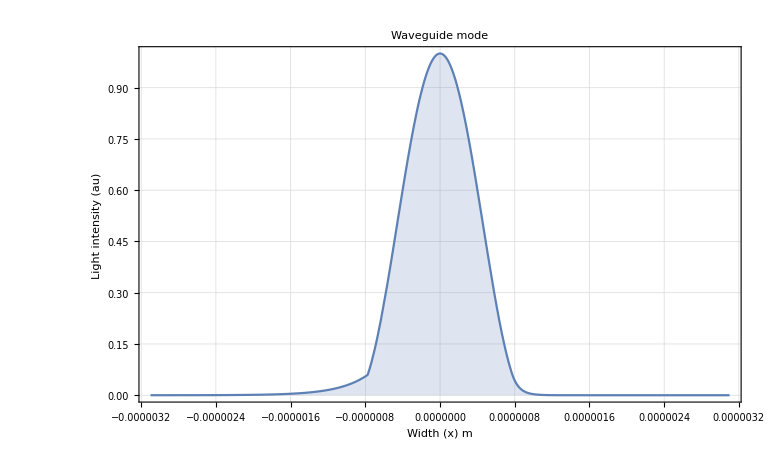

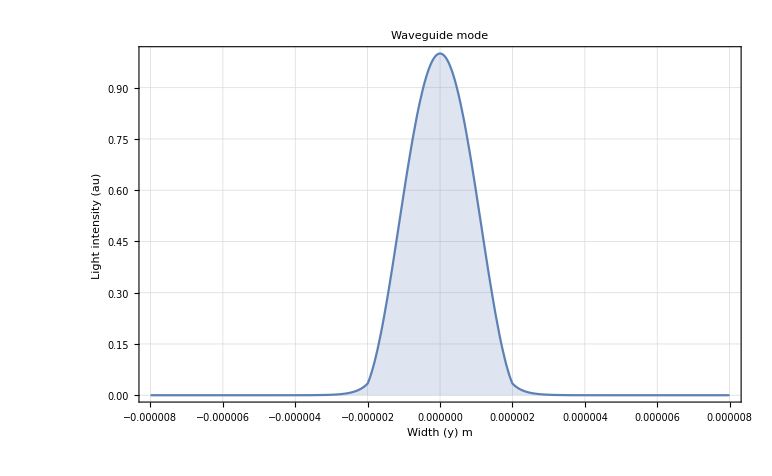

```mathematica
Clear[modex,modey, kzxy,k2x,α1x,α3x,k2y,α3y] 
kzxy:=2π×neffxy/λ; (*the propagation constant in the z direction*)
k2x:=Sqrt[ω^2×μ0×ϵ2-kzxy^2](*the x direction k value in layer 2*)
α1x:=Sqrt[kzxy^2-ω^2×μ0×ϵ1](*the x direction k value in layer 1*)
α3x:=Sqrt[kzxy^2-ω^2×μ0×ϵ3](*the x direction k value in layer 3*)
k2y:=k0 √(2×Δn×n3×bxz(1-byz))(*the y direction k value in layer 2*)
α3y:=k0 √(2Δn×n3×bxz×byz)(*the y direction k value in layer 3*)
modex[x_]:=Cos[k2x x]/;(-d/2≤x&&x≤d/2)(*the electric field x distribution in layer 2*)
modex[x_]:=Cos[d/2×k2x]*Exp[-α1x(x-d/2)]/;(x>d/2)(*the electric field x distribution in layer 1*)
modex[x_]:=Cos[-d/2×k2x]*Exp[α3x*(x+d/2)]/;(x<-d/2)(*the electric field x distribution in layer 3*)
Plot[(modex[x])^2,{x,-2d,2d}, PlotRange->All, Frame->True,PlotLabel->"Waveguide mode",AxesStyle->Thin,GridLines->Automatic,LabelStyle->{FontFamily->"Times New Roman",24,GrayLevel[0]},FrameLabel->{" Width (x) m ","Light intensity (au) "},FrameStyle->Thick,Filling->Axis, FillingStyle->Automatic](*Plot the light intensity as a function of x *)
modey[y_]:=Cos[k2y y]/;(-W/2≤y&&y≤W/2)(*the electric field y distribution in layer 2*)
modey[y_]:=Cos[W/2×k2y]*Exp[-α3y(y-W/2)]/;(y>W/2)(*the electric field y distribution in layer 3*)
modey[y_]:=Cos[-W/2×k2y]*Exp[α3y*(y+W/2)]/;(y<-W/2)(*the electric field -y distribution in layer 3*)
Plot[(modey[y])^2,{y,-2W,2W}, PlotRange->All, Frame->True,PlotLabel->"Waveguide mode",AxesStyle->Thin,GridLines->Automatic,LabelStyle->{FontFamily->"Times New Roman",24,GrayLevel[0]},FrameLabel->{" Width (y) m ","Light intensity (au) "},FrameStyle->Thick,Filling->Axis, FillingStyle->Automatic] (*Plot the light intensity as a function of y *)
```

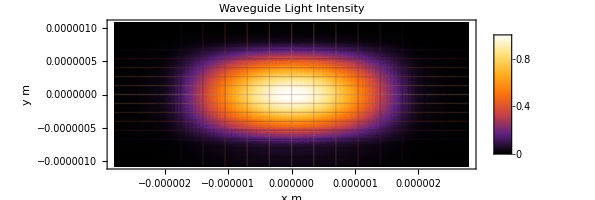

```mathematica
(* 2D plot of the waveguide mode *)
ScaleXY:=0.7;
DensityPlot[(modey[y]×modex[x])^2,{y,-ScaleXY W,ScaleXY W},{x,-ScaleXY d,ScaleXY d},PlotLabel-> "Waveguide Light Intensity",Axes->True,AxesLabel->{"x m","y m"},PlotPoints->100, Mesh->Automatic,AspectRatio->Automatic, ColorFunction->"SunsetColors",PlotLegends->Automatic]
```